# UniDyn--Demo-07.nb

Aritro Sinha Roy
as836@cornell.edu
Cornell University

Abstract:  This demonstration notebook loads the UniDyn package and illustrate its use in simulating selective quantum coherence generation from two spin-1/2 particles in a multi-pulse experiment.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$UniDynPath ="C:\\Users\\as836\\Documents\\GitHub\\UniDyn\\unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
(* $Path = AppendTo[$Path,$NCPath];*)
$Path = AppendTo[$Path,$UniDynPath];
FindFile["UniDyn`"]
```

C:\Users\as836\Documents\GitHub\UniDyn\unidyn\UniDyn.m

Now that we are confident that the path is set correctly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True; (* Set to load quietly *)
Needs["UniDyn`"]
```

## Three spin-1/2 particles: Selective quantum coherence generation

Create a  single-spin system to play with.

```mathematica
Needs["UniDyn`"];
Clear[Ix1, Iy1, Iz1,Δ1,Ix2, Iy2, Iz2,Δ2,Ix3, Iy3, Iz3,Δ3,a12,a13,a23,ω]
Quiet[
CreateScalar[{Δ1,Δ2,Δ3,a12,a13,a23,ω}];
CreateOperator[{{Ix1, Iy1, Iz1},{Ix2,Iy2,Iz2},{Ix3,Iy3,Iz3}}];
SpinSingle$CreateOperators[Ix1, Iy1, Iz1,1/2];
SpinSingle$CreateOperators[Ix2, Iy2, Iz2,1/2];
SpinSingle$CreateOperators[Ix3, Iy3, Iz3,1/2];
]
```

```mathematica
SimplifyingEvolver[H_,t_,ρ$0_]:=  

(*   H = Hamiltonian operator *)
(*   t = time varaible *)
(* ρ$0 = initial density operator *)

Evolver[H, t, ρ$0]//Simplify// ExpToTrig
```

Define free-evolution and pulse propagators

```mathematica
(* Extraction of operators from an expression *)
op$extA[elem_]:=Module[{pos,ans},
pos=Position[OperatorQ/@Level[elem,1],True];
ans=Level[elem,1][[pos[[1,1]]]];
Return[ans];
]

op$ext[elem_]:=Module[{ans},
If[Dimensions[elem]==={},ans = elem,
ans = Check[op$extA[elem],If[OperatorQ@elem,elem,None]]//Quiet];
Return[ans];
]
```

```mathematica
(* Group and simplify expressions by operators *)
col$op[exp_,op_,s_]:= Module[{op$l,exp$l,dim,exp$s,j},exp$l = exp//Expand;dim = Dimensions[exp$l][[1]];op$l = {};For[j=1,j≤dim,j++,op$l = Append[op$l,op$ext[exp$l[[j]]]]];op$l = DeleteDuplicates[op$l];If[op==1,exp$s = Simplify[#,TimeConstraint->s]&/@Collect[exp$l,op$l],If[op==2,exp$s = FullSimplify[#,TimeConstraint->s]&/@Collect[exp$l,op$l],exp$s = Collect[exp$l,op$l]]];Return[exp$s]]
```

```mathematica
(* Define free-evolution under the influence of the secular spin Hamiltonian *)
FreeEvolution[ρ_,t_, sim_]:=(*ρ=density operator*)(*t=time[s]*)(* sim = 1: Simplify, 2: FullSimplify *)
Module[{dim, A, B, Anew,ρnew},
dim = Dimensions[ρ][[1]];
ρnew = ((ρ//SimplifyingEvolver[Δ1 Iz1,t,#]&//SimplifyingEvolver[Δ2 Iz2,t,#]&//SimplifyingEvolver[Δ3 Iz3,t,#]&//SimplifyingEvolver[a12 Mult[Iz1,Iz2],t,#]&//SimplifyingEvolver[a13 Mult[Iz1,Iz3],t,#]&//SimplifyingEvolver[a23 Mult[Iz2,Iz3],t,#]&)//Expand//MultSort)//Expand;
ρnew= col$op[ρnew,sim,1]; (* Timeconstraint = 1 for simplification *)
Return[ρnew];
]
```

```mathematica
(* Define non-selective ideal δ-pulses with flip angle θ and phase ϕ *)
Pulse[ρ_,θ_,ϕ_,sim_]:=(*ρ=density operator*)(*θ=flip angle*)(*ϕ=phase*)
 Module[{dim, A, B, Anew,ρnew},
ρnew = ((ρ//SimplifyingEvolver[Ix1 Cos[ϕ]+Iy1 Sin[ϕ],θ,#]&//SimplifyingEvolver[Ix2 Cos[ϕ]+Iy2 Sin[ϕ],θ,#]&//SimplifyingEvolver[Ix3 Cos[ϕ]+Iy3 Sin[ϕ],θ,#]&)//Expand//MultSort)//Expand//Quiet;
ρnew= col$op[ρnew,sim,1]; (* Timeconstraint = 1 for simplification *)
Return[ρnew];
]
```

Overview of the pulse-sequence

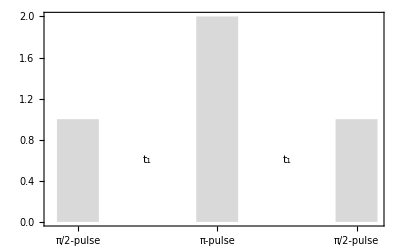

```mathematica
text$1 = Text[Style["t_1",Large],{2.5,0.6}];
text$2 = Text[Style["t_1",Large],{5.5,0.6}];
gr$ = Graphics[{text$1,text$2}];
pp$ = BarChart[{1,Missing[],Missing[],2,Missing[],Missing[],1},ChartStyle->{"Pastel",LightGray},ChartBaseStyle->EdgeForm[None],
ChartLabels->{"π/2-pulse","","","π-pulse","","","π/2-pulse"},LabelStyle->{FontSize->22},
Frame->{True,True,False,False},FrameTicksStyle->{Opacity[0],Opacity[1]},FrameStyle->Opacity[0],
(* Axes->{True,False},*) ImageSize->400];
DeleteCases[pp$,_Line?(Not@*FreeQ[_Offset]),All];
Show[pp$,gr$]
```

Density operator evolution

```mathematica
AbsoluteTiming[
(* Subscript[ρ, 0] is the density operator at thermal equilibrium *)
ρ0 = Iz1; 

(* Application of the first π/2-pulse with its phase set to {0, π/2, π, 3 π/2} *)
ρ1 = Pulse[ρ0,π/2,ϕ1,2]//Quiet;

(* A free-evolution period *)
ρ2 = FreeEvolution[ρ1,t1,2]//Quiet;

(* Application of the first refocusing π-pulse with its phase set to {0, π/2, π, 3 π/2} *)
ρ3 = 0;
dim = Dimensions[ρ2][[1]];
Monitor[
For[k=1,k<=dim,k++,
ρ = Pulse[ρ2[[k]],π,ϕ2,1];
AddTo[ρ3,ρ]],
Row[{ProgressIndicator[k,{1,dim}],NumberForm[(1.*k)/dim,{2,2}]},"  % ρ3 calculated = "]];
ρ3F = col$op[ρ3,2,1];

(* The second free-evolution period *)
ρ4 = 0;
dim = Dimensions[ρ3F][[1]];
Monitor[
For[k=1,k<=dim,k++,
ρ = FreeEvolution[ρ3F[[k]],t1,1];
AddTo[ρ4,ρ]],
Row[{ProgressIndicator[k,{1,dim}],NumberForm[(1.*k)/dim,{2,2}]},"  % ρ4 calculated = "]];
ρ4F = col$op[ρ4,2,1];

(* The second π/2-pulse to create multi-quantum coherence *)
ρ5 = 0;
dim = Dimensions[ρ4F][[1]];
Monitor[
For[k=1,k<=dim,k++,
ρ = Pulse[ρ4F[[k]],π/2,ϕ3,1];
AddTo[ρ5,ρ]],
Row[{ProgressIndicator[k,{1,dim}],NumberForm[(1.*k)/dim,{2,2}]},"  % ρ5 calculated = "]];
ρ5F = col$op[ρ5,2,1];][[1]]
```

226.19

In general, setting ϕ_1 = ϕ_2 = ϕ_3 generates only even order coherences

```mathematica
ρEvenQC = col$op[ρ5F/.{ϕ2->ϕ1, ϕ3->ϕ1},2,1]
```

Iz1 Cos[a12 t1] Cos[a13 t1]+2 Cos[a13 t1] Cos[ϕ1]^2 Mult[Ix1,Iy2] Sin[a12 t1]+2 Cos[a12 t1] Cos[ϕ1]^2 Mult[Ix1,Iy3] Sin[a13 t1]-4 Cos[ϕ1]^2 Mult[Iz1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]-2 Cos[a13 t1] Mult[Iy1,Ix2] Sin[a12 t1] Sin[ϕ1]^2-2 Cos[a12 t1] Mult[Iy1,Ix3] Sin[a13 t1] Sin[ϕ1]^2-4 Mult[Iz1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2-Cos[a13 t1] Mult[Ix1,Ix2] Sin[a12 t1] Sin[2 ϕ1]+Cos[a13 t1] Mult[Iy1,Iy2] Sin[a12 t1] Sin[2 ϕ1]-Cos[a12 t1] Mult[Ix1,Ix3] Sin[a13 t1] Sin[2 ϕ1]+Cos[a12 t1] Mult[Iy1,Iy3] Sin[a13 t1] Sin[2 ϕ1]+2 Mult[Iz1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[2 ϕ1]+2 Mult[Iz1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[2 ϕ1]

Let’s plot the signals for a set of zero and double quantum coherences with ϕ_1 varying from 0 to 3×π/2

```mathematica
zq$A = -4 Cos[ϕ1]^2 Mult[Iz1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]-4 Mult[Iz1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2;
dq$A = 2 Cos[a13 t1] Cos[ϕ1]^2 Mult[Ix1,Iy2] Sin[a12 t1]-2 Cos[a13 t1] Mult[Iy1,Ix2] Sin[a12 t1] Sin[ϕ1]^2;
(* Assign values to the dipolar constants *)
dip$ = {a13->2., a12->1.}; (* in MHz *)
zq$A$N = zq$A/.dip$;
dq$A$N = dq$A/.dip$;
```

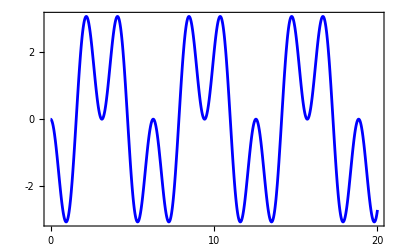
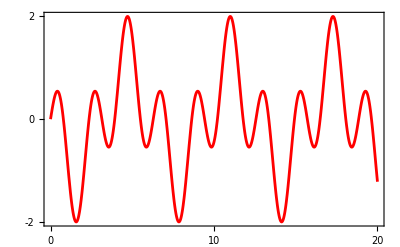
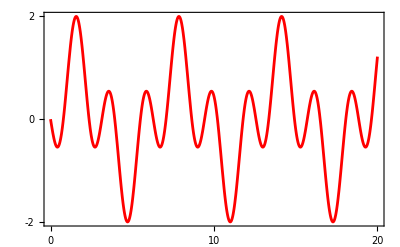
ZQ
Coherence | -Graphics- | -Graphics- | -Graphics- | -Graphics-
DQ
Coherence | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(* ZQCs vs. phase Subscript[ϕ, 1] *)
zqps$ = {};
zqclrs$ = {Blue,Blue,Blue,Blue};
For[j=1,j<=4,j++,
p$ = Plot[zq$A$N/.{ϕ1->(j-1)*π/2}/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1},{t1,0,20}, PlotRange->All, PlotStyle->zqclrs$[[j]], 
AxesOrigin->{0,-3},Frame->True,FrameTicks->{{{-2,0,2},None},{{0,10,20},None}},
FrameStyle->Directive[Thick,Gray,12]];
AppendTo[zqps$, p$];
];
(* DQCs vs. phase *)
dqps$ = {};
dqclrs$ = {Red,Red,Red,Red};
For[j=1,j<=4,j++,
p$ = Plot[dq$A$N/.{ϕ1->(j-1)*π/2}/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1},{t1,0,20}, PlotRange->All, PlotStyle->dqclrs$[[j]], 
AxesOrigin->{0,-3},Frame->True,FrameTicks->{{{-2,0,2},None},{{0,10,20},None}},
FrameStyle->Directive[Thick,Gray,12]];
AppendTo[dqps$, p$];
];
(* Combined plot of ZQC & DQC vs. Subscript[ϕ, 1] *)
plots$ = Transpose[{zqps$,dqps$}];
ylabels=Text[Style[#,Large]]&/@{"ZQ\nCoherence","DQ\nCoherence"};
Grid[Transpose[Join[{ylabels},plots$]]]
```

Note that the DQ coherence signal alternately goes in- and out-of-phase, while the ZQ signal remains in-phase throughout. Thus, adding the four signals will produce pure ZQ coherence while addition after multiplying the signals by {+1, -1, +1, -1} would produce pure DQ coherence.

We apply the phase cycle to the expression ρ5F to separate ZQ and DQ coherences:

```mathematica
(* Zero quantum coherence selection *)
ρ5$ZQ = 1/4*col$op[Sum[ρ5F/.{ϕ2->ϕ1,ϕ3->ϕ1}/.ϕ1->j*π/2,{j,0,3,1}]//Expand,2,1]//Expand
```

Iz1 Cos[a12 t1] Cos[a13 t1]+Cos[a13 t1] Mult[Ix1,Iy2] Sin[a12 t1]-Cos[a13 t1] Mult[Iy1,Ix2] Sin[a12 t1]+Cos[a12 t1] Mult[Ix1,Iy3] Sin[a13 t1]-Cos[a12 t1] Mult[Iy1,Ix3] Sin[a13 t1]-2 Mult[Iz1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]-2 Mult[Iz1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]

```mathematica
(* Double quantum coherence selection *)
ρ5$DQ = 1/4*col$op[Sum[(-1)^j*ρ5F/.{ϕ2->ϕ1,ϕ3->ϕ1}/.ϕ1->j*π/2,{j,0,3,1}]//Expand,2,1]//Expand
```

Cos[a13 t1] Mult[Ix1,Iy2] Sin[a12 t1]+Cos[a13 t1] Mult[Iy1,Ix2] Sin[a12 t1]+Cos[a12 t1] Mult[Ix1,Iy3] Sin[a13 t1]+Cos[a12 t1] Mult[Iy1,Ix3] Sin[a13 t1]+2 Mult[Iz1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]-2 Mult[Iz1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]

On the other hand, setting ϕ_1 = ϕ_2 = ϕ_3-π/2 generates only odd order coherences

```mathematica
ρOddQC = col$op[ρ5F/.{ϕ2->ϕ1, ϕ3->ϕ1+π/2},2,1]
```

Iy1 Cos[a12 t1] Cos[a13 t1] Cos[ϕ1]+2 Cos[a13 t1] Cos[ϕ1] Mult[Iz1,Ix2] Sin[a12 t1]+2 Cos[a12 t1] Cos[ϕ1] Mult[Iz1,Ix3] Sin[a13 t1]-4 Cos[ϕ1]^3 Mult[Iy1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]-Ix1 Cos[a12 t1] Cos[a13 t1] Sin[ϕ1]+2 Cos[a13 t1] Mult[Iz1,Iy2] Sin[a12 t1] Sin[ϕ1]+2 Cos[a12 t1] Mult[Iz1,Iy3] Sin[a13 t1] Sin[ϕ1]+4 Cos[ϕ1]^2 Mult[Ix1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]-4 Cos[ϕ1]^2 Mult[Iy1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]-4 Cos[ϕ1]^2 Mult[Iy1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]+4 Cos[ϕ1] Mult[Ix1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2+4 Cos[ϕ1] Mult[Ix1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2-4 Cos[ϕ1] Mult[Iy1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2+4 Mult[Ix1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^3

Let’s plot a single quantum coherence and the triple quantum coherence signals with ϕ_1 varying from 0 to 3×π/2

```mathematica
-Mult[Ix1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1]-Mult[Ix1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1]-Mult[Iy1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]+Mult[Iy1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]
```

```mathematica
sq$A = Iy1 Cos[a12 t1] Cos[a13 t1] Cos[ϕ1]-Ix1 Cos[a12 t1] Cos[a13 t1] Sin[ϕ1];
tq$A = -4 Cos[ϕ1]^3 Mult[Iy1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]+4 Cos[ϕ1] Mult[Ix1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2+4 Cos[ϕ1] Mult[Ix1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2-4 Cos[ϕ1] Mult[Iy1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2;
(* Assign values to the dipolar constants *)
dip$ = {a13->2., a12->1.}; (* in MHz *)
sq$A$N = sq$A/.dip$;
tq$A$N = tq$A/.dip$;
```

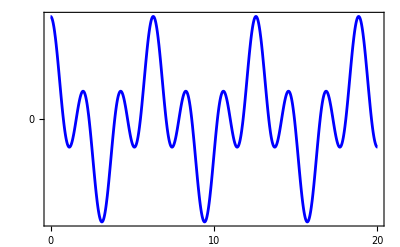
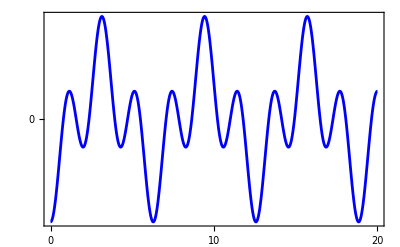
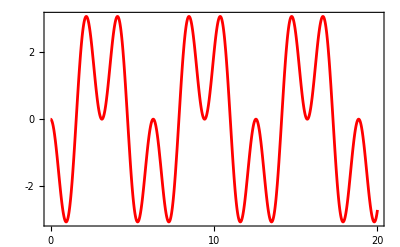
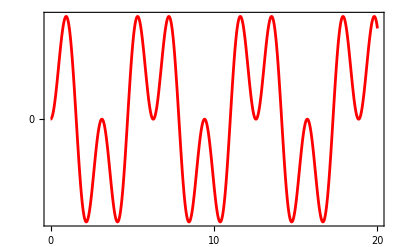
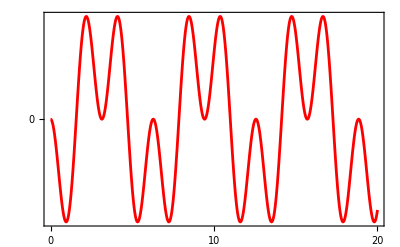
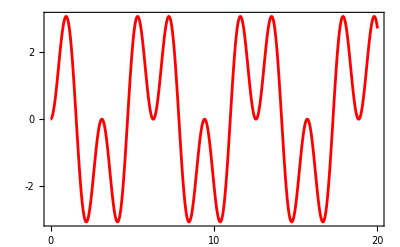
SQ
Coherence | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TQ
Coherence | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(* SQCs vs. phase Subscript[ϕ, 1] *)
sqps$ = {};
sqclrs$ = {Blue,Blue,Blue,Blue,Blue,Blue};
For[j=1,j<=6,j++,
p$ = Plot[sq$A$N/.{ϕ1->(j-1)*π/3}/.{ Ix1->1,Iy1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1},{t1,0,20}, PlotRange->All, PlotStyle->sqclrs$[[j]], 
AxesOrigin->{0,-3},Frame->True,FrameTicks->{{{-2,0,2},None},{{0,10,20},None}},
FrameStyle->Directive[Thick,Gray,12]];
AppendTo[sqps$, p$];
];
(* TQCs vs. phase *)
tqps$ = {};
tqclrs$ = {Red,Red,Red,Red,Red,Red};
For[j=1,j<=6,j++,
p$ = Plot[tq$A$N/.{ϕ1->(j-1)*π/3}/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1},{t1,0,20}, PlotRange->All, PlotStyle->tqclrs$[[j]], 
AxesOrigin->{0,-3},Frame->True,FrameTicks->{{{-2,0,2},None},{{0,10,20},None}},
FrameStyle->Directive[Thick,Gray,12]];
AppendTo[tqps$, p$];
];
(* Combined plot of SQC & TQC vs. Subscript[ϕ, 1] *)
plots$ = Transpose[{sqps$,tqps$}];
ylabels=Text[Style[#,Large]]&/@{"SQ\nCoherence","TQ\nCoherence"};
Grid[Transpose[Join[{ylabels},plots$]]]
```

Again, note that if the receiver phase is set to 0 and π alternatively, we will get pure TQ coherence, while the SQ signals would cancel.

We apply the 6-step phase cycle to the expression ρ5F to select only TQ coherence:

```mathematica
(* Triple quantum coherence selection *)
ρ5$TQ = 1/6*col$op[Sum[(-1)^j*ρ5F/.{ϕ2->ϕ1,ϕ3->ϕ1+π/2}/.ϕ1->j*π/3,{j,0,5,1}]//Expand,2,1]//Expand
```

-Mult[Ix1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1]-Mult[Ix1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1]-Mult[Iy1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]+Mult[Iy1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]

To select only single quantum coherence, we apply the following 2-step phase cycle by setting ϕ_2 to 0 and π :

```mathematica
(* Single quantum coherence selection *)
ρ5$SQ = 1/2*col$op[Sum[ρ5F/.{ϕ3->ϕ1+π/2}/.{ϕ1->0,ϕ2->j*π},{j,0,1,1}]//Expand,2,1]//Expand
```

Iy1 Cos[a12 t1] Cos[a13 t1]+2 Cos[a13 t1] Mult[Iz1,Ix2] Sin[a12 t1]+2 Cos[a12 t1] Mult[Iz1,Ix3] Sin[a13 t1]-4 Mult[Iy1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]